```mathematica
(*Initializes a sandpile given a distribution and a maximum height*)
InitializePile[size_,initdistr_,max_]:=Module[
{pile},
(*Initialize distributions *)
Switch[initdistr,
"Uniform",
pile = Table[RandomInteger[max],size];,
"Zero",
pile = Table[0,size];,
"Critical",
pile = Table[size*max - (i-1)*max,{i,1,size}];
];
(*Create the pile and return *)
Return[pile];
];
```

```mathematica
(*Determines where to drop the next grain(s) of sand based on a given distribution*)
fill[grid_,max_,generatingdistr_]:=Module[{size,g,offset,center,x,y},
size=Length[grid];
Switch[generatingdistr,
"Fill",
offset=Table[If[grid[[i]]<max,1,0],{i,1,size}];,
"Left",
offset = Table[If[i==1,1,0],{i,1,size}];,
"Centered",
center = Round[size/2];
If[size==5,center++];
offset = Table[If[i==center,1,0],{i,1,size}];,
"Uniform",
x=RandomInteger[size];
offset = Table[If[i==x,1,0],{i,1,size}];,
"None",
offset=Table[0,size];
];
Return[offset];
];
```

```mathematica
(*Determines the offset caused by an avalanche, and also determines whether the 
avalanches will continue*)
Avalanche[grid_,max_,touched_]:=Module[{gs,cites,n,topples,offset,i,j,touchupdate},
n=Length[grid];
topples=0;
touchupdate = touched;
(* Find the location of the avalanches. *)
gs = PadRight[grid,n+1];
cites=Table[
If[gs[[i]]-gs[[i+1]]>max,
topples++;
-1
,
0]
,{i,1,n}];
(*Add 1 to cells adjacent to toppled cells *)
offset=Table[0,n+1];
touchupdate = PadRight[touchupdate,n+1];
For[i=1,i≤n,i++,
If[cites[[i]]==-1,
offset[[i+1]] += 1;
touchupdate[[i]] = 1;
touchupdate[[i+1]] = 1;
]
];
offset=PadRight[offset,n];
touchupdate = PadRight[touchupdate,n];
(*Combined the toppled cells with their neighbors to find the overall offset *)
offset +=cites;
(*Determine whether or not we need to check avalanche again*)
If[topples==0,
Return[{offset,False,touchupdate,topples}],
Return[{offset,True,touchupdate,topples}]
];
];
```

```mathematica
(*Generate SandPile Data lol*)
(*playing around with the dynamic module is too slow*)
GSPD[size_,initialdistr_,criticalvalue_,generatingdistr_,iters_]:=Module[
{i=0,
m=InitializePile[size,initialdistr,criticalvalue],
maxval=0,
avgheight = 0,
totaltopples=0,
topples = 0,
avalanching=False,
avalanche=InitializePile[size,"Zero",criticalvalue],
touched = InitializePile[size,"Zero",criticalvalue],
avalancheiters = 0,
avalanchelength = {},
avalanchesize = {},
running = True,
sandpileplot
},
If[Max[m]>maxval,maxval=Max[m]];
If[maxval==0,maxval=1];
avgheight=N[Mean[m]];
sandpileplot=BarChart[m
,ImageSize->{300,300}
,PlotLabel->i
,PlotRange->{0,maxval}];
(*Check if we are running. Allows for manual stop *)
Monitor[
While[i≤iters,
(*Check if we need to calculate avalanches*)
(*This is checked after every time a new grain is added *)
If[avalanching,
{avalanche,avalanching,touched,topples}=Avalanche[m,criticalvalue,touched];
m = m + avalanche;
(*We can run again once there are no more topples*)
If[avalanching,
avalancheiters ++;
running=False;
,
(*Record the corresponding avalanche size and length *)
avalanchelength = Join[{{i,avalancheiters}},avalanchelength];
avalanchesize = Join[{{i,Total[touched]}},avalanchesize];
(*Reset the number of touched nodes and avalanche iters*)
touched = InitializePile[size,"Zero",criticalvalue];
avalancheiters = 0;
running=True;
];
];
If[running,
avgheight=N[Mean[m]];
i=i+1;
m = m+ fill[m,criticalvalue,generatingdistr];
If[Max[m]>maxval,maxval=Max[m]];
avalanching=True;
];
If[Mod[i,5000]==0,
sandpileplot=BarChart[m
,ImageSize->{300,300}
,PlotLabel->i
,PlotRange->{0,maxval}];
];
];
,sandpileplot];
Print[sandpileplot];
Return[{avalanchelength,avalanchesize}];
];
```

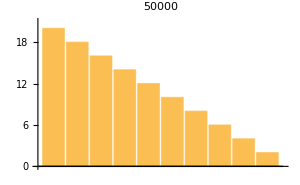

```mathematica
{al,as}=GSPD[10,"Zero",2,"Uniform",50000];
```

```mathematica
GenerateHistograms[avalanchelength_,avalanchesize_]:=Module[
{al,as,
lenhl,sizehl,
lendata,sizedata,
lenfit,sizefit,
lenfreq,sizefreq,
gg,imgsize},
imgsize=ImageSize->{500,500};
(*Turn our (time,value) tables into just the values*)
al=avalanchelength[[All,2]];
as=avalanchesize[[All,2]];
(*Create histogram data over our values*)
lenhl=HistogramList[al,{1}];
sizehl=HistogramList[as,{1}];
(*Creating a CDF*)
lenfreq=Table[{i,Log10[(Length[al]-Total[PadRight[lenhl[[2]],i]]+1)/Length[al]]},{i,1,Length[lenhl[[2]]]}];
(*sizedata=Transpose[{Drop[sizehl[[1]],-1],sizehl[[2]]}];*)
(*lenfit=FindFit[lenfreq,a (x)^(-tau),{a,tau},x];*)
(*sizefit=FindFit[Drop[sizedata,1],a (x)^(-tau)+c,{a,tau,c},x];*)
gg=GraphicsGrid[{{
Show[ListLogLinearPlot[lenfreq](*,Plot[a x^(-tau)/.lenfit,{x,0.1,Max[al]}]*)]
(*Show[Histogram[al,imgsize,ScalingFunctions->"Log",PlotRange->{0,5000}],LogPlot[a x^(-tau)+c/.lenfit,{x,0.1,Max[al]},AxesOrigin->{0,0}]]*)(*,
Show[Histogram[as,imgsize,ScalingFunctions->"Log"],LogLinearPlot[a x^(-tau)/.sizefit,{x,0.1,Max[as]},AxesOrigin->{0,0}]]*)
}}]
];
```

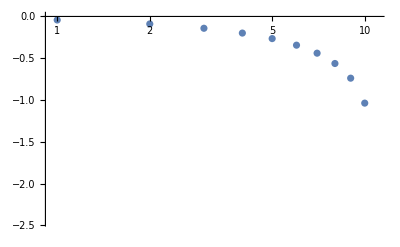

```mathematica
GenerateHistograms[al,as]
```

```mathematica
Chop
```

{1,2,3,4,5}